```mathematica
ψ[m_,n_,x_,y_]=Sin[n Pi x] Sin[m Pi y];
```

```mathematica
λ[m_,n_]= -(m^2 + n^2)Pi^2
```

(-m^2-n^2) π^2

```mathematica
c[m_,n_]= Integrate[ψ[m,n,x,y] 1,{x,0,1},{y,0,1}]/(λ[m,n] 1/4)
```

(4 (-1+Cos[m π]) (-1+Cos[n π]))/(m n (-m^2-n^2) π^4)

```mathematica
ϕ[x_,y_]= Sum[c[m,n]ψ[m,n,x,y],{m,1,10},{n,1,10}];
```

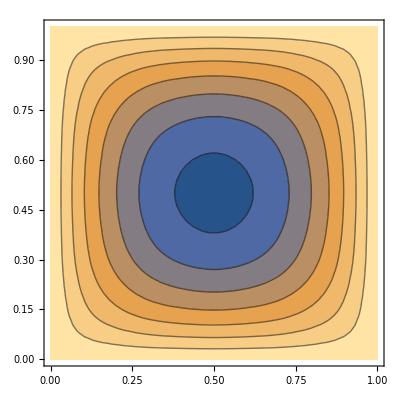

```mathematica
ContourPlot[ϕ[x,y],{x,0,1},{y,0,1}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{f''[y]-k^2 f[y]==2/a DiracDelta[y-y0]Sin[k x0],f[0]==0,f[b]==0},f[y],y]
```

{{f[y]→1/(a (-1+ⅇ^(2 b k)) k)ⅇ^(-k y-k y0) (ⅇ^(2 b k) HeavisideTheta[b-y0]-ⅇ^(2 b k+2 k y) HeavisideTheta[b-y0]-ⅇ^(2 k y0) HeavisideTheta[b-y0]+ⅇ^(2 k y+2 k y0) HeavisideTheta[b-y0]-ⅇ^(2 k y) HeavisideTheta[y-y0]+ⅇ^(2 b k+2 k y) HeavisideTheta[y-y0]+ⅇ^(2 k y0) HeavisideTheta[y-y0]-ⅇ^(2 b k+2 k y0) HeavisideTheta[y-y0]-ⅇ^(2 b k) HeavisideTheta[-y0]+ⅇ^(2 k y) HeavisideTheta[-y0]+ⅇ^(2 b k+2 k y0) HeavisideTheta[-y0]-ⅇ^(2 k y+2 k y0) HeavisideTheta[-y0]) Sin[k x0]}}

```mathematica
Simplify[%,0<y0<b]
```

{{f[y]→1/(a (-1+ⅇ^(2 b k)) k)ⅇ^(-k (y+y0)) (-(-1+ⅇ^(2 k y)) (ⅇ^(2 b k)-ⅇ^(2 k y0))+(-1+ⅇ^(2 b k)) (ⅇ^(2 k y)-ⅇ^(2 k y0)) HeavisideTheta[y-y0]) Sin[k x0]}}

```mathematica
f[y_]= f[y]/.%[[1]]
```

1/(a (-1+ⅇ^(2 b k)) k)ⅇ^(-k (y+y0)) (-(-1+ⅇ^(2 k y)) (ⅇ^(2 b k)-ⅇ^(2 k y0))+(-1+ⅇ^(2 b k)) (ⅇ^(2 k y)-ⅇ^(2 k y0)) HeavisideTheta[y-y0]) Sin[k x0]